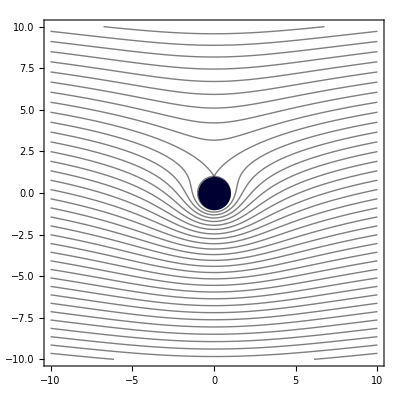
-Graphics-g=2

```mathematica
Options[fieldPlot]={"size"->10, Contours->40,"FieldLines"->80,"FieldLineStyle"->Directive[Black,Thick],"PotentialStyle"->{Directive[Thick,Darker[Cyan]]},ExclusionsStyle->None,Exclusions->None};

fieldPlot[g_,opts:OptionsPattern[]]:=Module[{im,re,xM,yM},xM=OptionValue["size"]; yM=xM;
disk= Graphics[{Darker[Blue,0.8],Disk[{0,0},{R,R}]}];
im=ContourPlot[Im[g[x+I y]],{x,-xM,xM},{y,-yM,yM},ContourShading->False,ContourStyle->OptionValue["FieldLineStyle"],Contours->OptionValue["FieldLines"],PerformanceGoal->"Quality",PlotPoints->100,MaxRecursion->2];
re=ContourPlot[Re[g[x+I y]],{x,-xM,xM},{y,-yM,yM},ContourShading->False,FrameLabel->{"Re(z)","Im(z)"},ContourStyle->OptionValue["PotentialStyle"],Contours->OptionValue[Contours],Exclusions->OptionValue[Exclusions],
ExclusionsStyle->OptionValue[ExclusionsStyle]];
Show[im,disk,Background->White,Frame->True,AspectRatio->Automatic]]
Clear[arg,log];
R=1; G=2;
size= 10;
arg[z_,σ_:-Pi]:=Arg[z Exp[-I (σ+Pi)]]+σ+Pi;
log[z_,σ_:-Pi/2]:=Log[Abs[z]]+I arg[z,σ];
g[z_] := z+R^2/z+log[z]/I*G;
s=Labeled[fieldPlot[g,"size"->size],"g="~~ToString[G]~~""]
SetDirectory[NotebookDirectory[]];
Export["plot"~~ToString[G]~~".pdf",s,"PDF","AllowRasterization"->False];
```